# Arnoldi Iteration

The Arnoldi Iteration is an iterative reinterpretation of the procedure to generate the Hessenberg decomposition of a general matrix. It is used to generate a small Upper Hessenberg matrix H that approximates large eigenvalues of a big matrix A

## Krylov Subspaces and the Arnoldi Iteration

The n dimensional Krylov space defined by A and b is 
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b})
The Arnoldi Iteration below constructs an orthogonal basis (a tall skinny orthogonal matrix Q∈ℝ^(m×n)) for the Krylov space and while building an “expanded” Upper Hessenberg matrix H that describes the action of A on Q.

Arnoldi Iteration
input b 
q_1=b/norm(b)
for n in 1:∞
	w = A.q_n
	for k in 1:n
		H_(k,n)=q_k.w
		w=w-H_(k,n)q_k
	end
	H_(n+1,n)=norm(w)
	q_(n+1)=w/norm(w)
…

This is easy to code.  I am writing this as a single step going from n⟶n+1.

The input arguments are A, the m×n orthogonal basis Q, and the (n+1)×n expanded upper Hessenberg matrix H.

Outputs are the new m×(n+1) orthogonal basis and (n+2)×(n+1) expanded upper Hessenberg matrix.

The argument we did to show that the Hessenberg decomposition was uniquely defined by the first column of Q might be useful here.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,w,hCol,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+2,n+1}];
w=A.Q⟦All,n⟧;
hCol=Table[
q=Q⟦All,k⟧;
HNew⟦k,n+1⟧=q.w;
w=w-HNew⟦k,n+1⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/Norm[w];
{Join[Qᵀ,{w}]ᵀ,HNew}
]
```

{{12,1},{2,1}}

{{12,2},{3,2}}

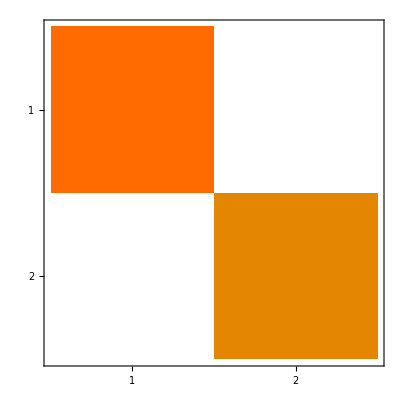
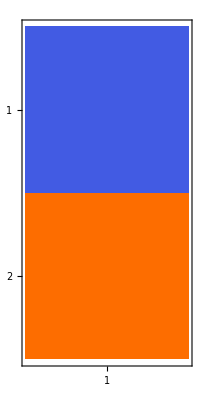
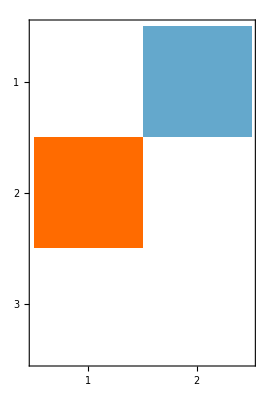

```mathematica
{m,n}={12,1};
{A,Q}=RandomReal[{-1,1},{2,m,m}];
Q=Orthogonalize[Q]⟦All,1;;n⟧;
H=UpperTriangularize[RandomReal[{-1,1},{n+1,n}],-1];
Map[Dimensions,{Q,H}]
{QNew,HNew}=Arnoldi[A][{Q,H}];
Map[Dimensions,{QNew,HNew}]
Map[MatrixPlot,{Chop[QNewᵀ.QNew],H,HNew}]
```

{{12,3},{4,3}}

{{4,3},{3,1}}

ArrayFlatten::match: ArrayFlatten[{{{{0.914142,0.930174,-0.729798},{0.283223,-0.880653,0.160869},{0.,-0.492323,0.191487},{0.,0.,-0.940627}},«1»},«1»}] fails the matching condition for ArrayFlatten[a,n]: if b = a[[i_1,i_2,...,i_n]], c = a[[j_1,j_2,...,j_n]], Head[a] == Head[b] == Head[c], Length[Dimensions[b]] >= n, Length[Dimensions[c]] >= n, and i_k = j_k, then Dimensions[b][[k]] must equal Dimensions[c][[k]]. Here the condition fails for k = 1 and i_k = j_k = 1.

{{12,3},{12,4},{4,3},{1}}

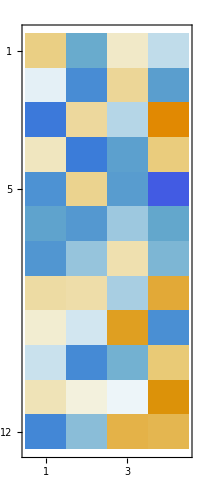

```mathematica
{QNew,HNew}=Arnoldi[A][{Q,H}];
Map[Dimensions,{Q,QNew,H,HNew}]
MatrixPlot[QNew]
```